Lo que quiero hacer es integrar funciones de densidad

```mathematica
Las funciones de densidad tienen cierta formula. Las voy a multiplicar y dsp se hace la integral en todo el espacio. Habria que ver una expresion que integre a uno y este multiplicado por su "factor". Despues, este factor puede estar relacionado a los valores de empleo de las plantas, por ejemplo.LinguisticAssistant
```

```mathematica
fx[x_,b_, m_,t_]:= t Exp[-Abs[x - m]/b]/(2b)
```

```mathematica
Integrate[fx[x, 1, 0, 1],{x, -Infinity, Infinity}]
```

1

```mathematica
fx[x, b1, x0, t1]*fx[x, b2, x0 +d, t2]
```

(ⅇ^(-Abs[x-x0]/b1-Abs[-d+x-x0]/b2) t1 t2)/(4 b1 b2)

```mathematica
b = .1;d=1;
```

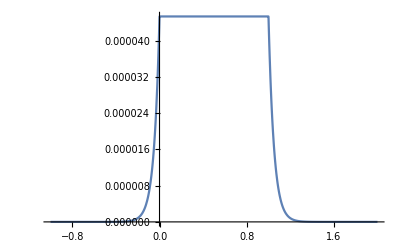

```mathematica
Plot[Exp[-(Abs[x]+Abs[-d+x])/b],{x, -1, 2}]
```

```mathematica
fx[x_,y_,x0_, y0_, b_, t_]:= t Exp[-Norm[{x, y}-{x0, y0}]/b]/(2Pi b)
```

```mathematica
b=1;
t=1;
Integrate[fx[x,y,0, 0, b, t],{x, -Infinity, Infinity}, {y, -Infinity, Infinity}]
```

1

```mathematica
Integrate[fx[x,y,1, 0, b, t]*fx[x,y,0, 0, b, t],{x, -Infinity, Infinity}, {y, -Infinity, Infinity}]
```

$Aborted

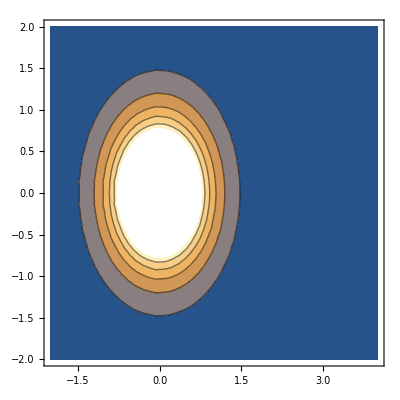

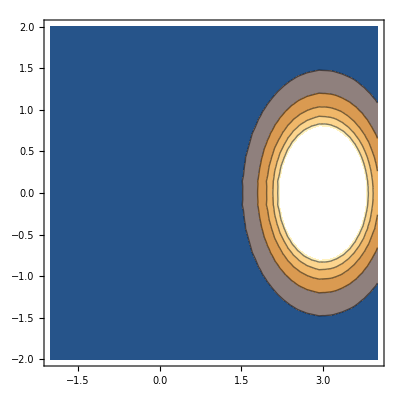

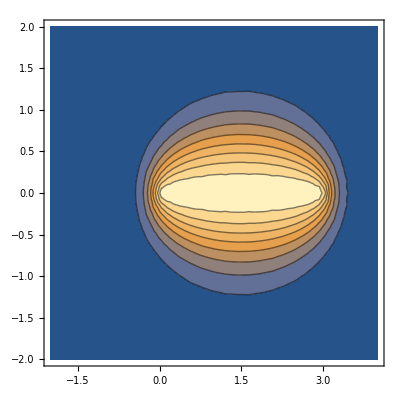

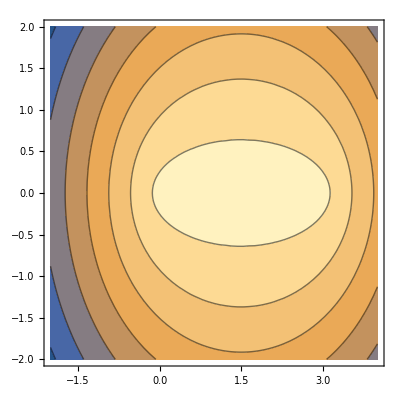

```mathematica
b1=.4;
b2=.4;
t=1;(*ContourPlot[Log[fx[x,y,0, 0, b1, t]*fx[x,y,1, 0, b2, t]], {x, -2, 4}, {y, -2, 2}]*)
ContourPlot[fx[x,y,0, 0, b1, t], {x, -2, 4}, {y, -2, 2}]
ContourPlot[fx[x,y,3, 0, b2, t], {x, -2, 4}, {y, -2, 2}]
ContourPlot[fx[x,y,0, 0, b1, t]*fx[x,y,3, 0, b2, t], {x, -2, 4}, {y, -2, 2}]
ContourPlot[Log[fx[x,y,0, 0, b1, t]*fx[x,y,3, 0, b2, t]], {x, -2, 4}, {y, -2, 2}]
```

```mathematica
fx[x_,y_,x0_, y0_, b_, t_]:= t Exp[-Norm[{x, y}-{x0, y0}]/b]/(2Pi b)
```

```mathematica
gx[x_,y_,x0_, y0_, s_, A_]:= A Exp[-Norm[{x, y}-{x0, y0}]^2/(2 s^2)]/(2 Pi s^2 )
```

```mathematica
Integrate[gx[x,y,0, 0, s, A],{x, -Infinity, Infinity}, {y, -Infinity, +Infinity}]
```

1

```mathematica
s1=.4;
s2=.4;
A=.;(*ContourPlot[Log[fx[x,y,0, 0, b1, t]*fx[x,y,1, 0, b2, t]], {x, -2, 4}, {y, -2, 2}]*)
ContourPlot[gx[x,y,0, 0, s1, A], {x, -2, 4}, {y, -2, 2}]
ContourPlot[gx[x,y,3, 0, s2, A], {x, -2, 4}, {y, -2, 2}]
ContourPlot[gx[x,y,0, 0, s1, A]*gx[x,y,3, 0, s2, A], {x, -2, 4}, {y, -2, 2}]
ContourPlot[Log[gx[x,y,0, 0, s1, A]*gx[x,y,3, 0, s2, A]], {x, -2, 4}, {y, -2, 2}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
Integrate[gx[x,y,0, 0, 2, A]*gx[x,y,d, 0, 2, A],{x, -Infinity, Infinity}, {y, -Infinity, Infinity}]
```

(A^2 ⅇ^(-1/8 Im[d]^2-Re[d]^2/16))/(16 π)

```mathematica
d=.
```

```mathematica
Expand[x^2 + (x-d)^2]
```

d^2-2 d x+2 x^2

```mathematica
prod[A1_, A2_, d_, s1_, s2_]:=(A1 A2 ⅇ^(-d^2/(2(s1^2+s2^2))))/((s1^2+s2^2)2 π)
```

```mathematica
A1=1;
A2=1;
s1=.25;
s2=.25;
Plot[{prod[A1, A2, d, s1, s2],gx[d,0,0, 0, s1, A1],gx[d,0,1, 0, s2, A2] }, {d, 0, 2}]+
```

```mathematica
+---***/
```